```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/code

```mathematica
sne=Import["data/neordered.txt","Table"];
```

```mathematica
sne[[1]]
```

{0.00819005,2.00852}

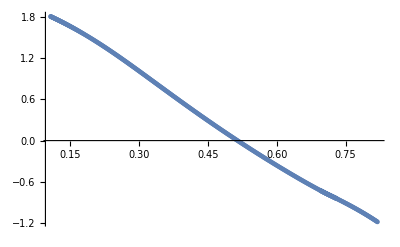

```mathematica
sneplt=Table[sne[[i]],{i,200,Length@sne-1800}];
snepl=ListPlot[sneplt,PlotRange->Full,ImageSize->Full]
```

```mathematica
fitted=LinearModelFit[sneplt,x,x]
```

FittedModel[2.2901-4.33005 x]

```mathematica
fittedPlt=Plot[Normal@fitted,{x,0,1}];
```

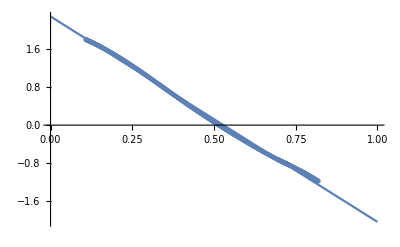

```mathematica
Show[fittedPlt,snepl,ImageSize->Full]
```